# The Orbitals of a Hydrogen Atom

## Plots, Wavefunctions, and Probability Clouds

Physics 230: Final Presentation

Aaron Jenkins and Daniel Manning

Brigham Young University

4/18/26

## The First Orbital

Hydrogen atoms are the simplest element on the periodic table, as well as the most plentiful element in the observable universe. Yet despite their ubiquity, a completed understanding of hydrogen atoms proved elusive to scientists. In this notebook, we plan to model the electron orbitals of hydrogen atoms and build up the functions that the Resource Function HydrogenWavefunction uses.

We start with the Bohr model and with the spherical harmonics to show what energy levels are. We can draw a Bohr model manually using Graphics objects and using the Bohr radius for the different energy levels, showing what n means. We can introduce the idea of positional uncertainty with Sin[Sqrt[x^2+y^2]]/Sqrt[x^2+y^2]
Heisenberg uncertainty using sums of sine waves, explaining the fundamental conflict with frequency and position.
1D, 2D, and 3D Particle in a Box--2D particle in a box: DensityPlot of two different sinusoidal plots, (Sin[m Pi*x]*Sin[n Pi*y])^2.

General idea: explain aspects of wavefunctions, until eventually using HydrogenWavefunction.

### The Bohr Model

Niels Bohr developed a model of the atom that built off Rutherford’s discovery of the atomic nucleus. While somewhat primitive by today’s standards and inaccurate in many ways, it was by far the best atomic model that had been suggested. His big breakthrough was the idea of quantized electron energy levels, or shells. He pictured electrons as orbiting the nucleus, like planets around a star, and much like planets, these electrons would have a fixed radius for a given energy level. These energy levels have a fixed energy differential between them, and for an electron to jump from one energy level to a higher one, it needs to absorb light of precisely the corresponding amount of energy. When the electrons drops back down to the initial energy level, it would emit a photon with that same amount of energy. The following graphic shows the first three electron shells at the predicted radii, shown in blue, orbiting the nucleus, shown in red. Note that the size of the nucleus is not to scale.

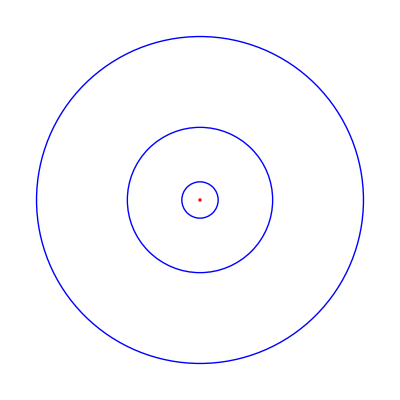

```mathematica
Graphics[{Red,Disk[{0,0},.05],Blue,Circle[{0,0},.529],Circle[{0,0},4*.529],Circle[{0,0},9*.529]}]
```

```mathematica
(*The Bohr model predicts that the energy of a given electron shell is given by E=-13.6/n^2, where n is the number of the energy level.*)
(*This function tells us the energy differential between two energy levels, n1 and n2. A positive value indicates that the electron dropped in energy from a high level to a lower level, while a negative value indicates that the electron absorbed energy to jump up from a low level to a higher level.*)
HydrogenBohrEnergy[n1_,n2_]:=Module[{n,m},
n=n1;
m=n2;
-13.6/n^2+13.6/m^2]
HydrogenBohrEnergy[1,2]
```

-10.2

The Bohr energy turned out to perfectly predict several things, most notably emission and absorption spectra of different elements. When certain elements are passed a lot of energy, they will only emit certain specific wavelengths of light, and when white light passes through a large cloud of a certain element, those same wavelengths of light get absorbed. Classical physics had no good explanation for this, but the Bohr model explained these absorption and emission lines. The wavelength of light may be calculated knowing its energy by the formula E=h*c/λ, where h and c are the physical constants and λ is the wavelength of light.

```mathematica
(*Given the energy of a photon in eV, this function returns the wavelength of that photon in nm*)
PhotonWavelength[e_]:=Module[{en},
en=e;
Abs[4.136*10^-15*3*10^8/en*10^9]]
PhotonWavelength[HydrogenBohrEnergy[2,3]]
PhotonWavelength[HydrogenBohrEnergy[2,4]]
```

656.894

486.588

As it turned out, the jumps between energy levels of the Bohr model perfectly corresponded to the energy of the emitted and absorbed photons. The Bohr model correctly predicted quantized electron energy levels, though it was not perfect. The assumption that the electrons orbited at a fixed speed and at a fixed radius was completely false.